# Section 4 演習問題

## 数理科学コース3年 09B10016 奥野彰文

## 演習課題4 .1

### 関数の設定

```mathematica
f[x_,t_]:=-x;
f1[x1_,x2_,t_]:=x2;
f2[x1_,x2_,t_]:=-x1;
```

```mathematica
euler::nonnegativeint="Nmax must be a non-negative integer."; (*Error message*)
```

### Euler法

```mathematica
euler[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
x1[j_]:=(x1[j]=x1[j-1]+dt f1[x1[j-1],x2[j-1],t]);
x2[j_]:=(x2[j]=x2[j-1]+dt f2[x1[j-1],x2[j-1],t]);
Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
```

```mathematica
eulergraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[euler[dt,Nmax,a1,a2],PlotRange->All]
```

### Heun法

```mathematica
heun[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,k1,k2,m1,m2,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
k1[j_]:=(k1[j]= f1[x1[j],x2[j],t]);
k2[j_]:=(k2[j]= f1[x1[j]+dt k1[j],x2[j]+dt k1[j],t+dt]);
m1[j_]:=(m1[j]=f2[x1[j],x2[j],t]);
m2[j_]:=(m2[j]=f2[x1[j]+dt m1[j],x2[j]+dt m1[j],t+dt]);
x1[j_]:=(x1[j]=x1[j-1]+dt/2(k1[j-1]+k2[j-1]));
x2[j_]:=(x2[j]=x2[j-1]+dt/2(m1[j-1]+m2[j-1]));
Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
```

```mathematica
heungraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[heun[dt,Nmax,a1,a2],PlotRange->All,PlotStyle->RGBColor[1,1,0]]
```

### Runge - Kutta法

```mathematica
runge[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,k1,k2,k3,k4,m1,m2,m3,m4,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
k1[j_]:=(k1[j]= f1[x1[j],x2[j],t]);
k2[j_]:=(k2[j]= f1[x1[j]+dt/2 k1[j],x2[j]+dt/2 k1[j],t+dt/2]);
k3[j_]:=(k3[j]=f1[x1[j]+dt/2 k2[j],x2[j]+dt/2 k2[j],t+dt/2]);
k4[j_]:=(k4[j]=f1[x1[j]+dt k3[j],x2[j]+dt k3[j],t+dt]);
m1[j_]:=(m1[j]=f2[x1[j],x2[j],t]);
m2[j_]:=(m2[j]=f2[x1[j]+dt/2 m1[j],x2[j]+dt/2 m1[j],t+dt/2]);
m3[j_]:=(m3[j]=f2[x1[j]+dt/2 m2[j],x2[j]+dt/2 m2[j],t+dt/2]);
m4[j_]:=(m4[j]=f2[x1[j]+dt m3[j],x2[j]+dt m3[j],t+dt]);
x1[j_]:=(x1[j]=x1[j-1]+dt/6(k1[j-1]+2 k2[j-1]+2 k3[j-1]+k4[j-1]));
x2[j_]:=(x2[j]=x2[j-1]+dt/6(m1[j-1]+2 m2[j-1]+2 m3[j-1]+m4[j-1]));
Table[{j dt,x1[j]},{j,0,Nmax}]
]
];
```

```mathematica
rungegraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[runge[dt,Nmax,a1,a2],PlotRange->All,PlotStyle->RGBColor[0,0,0]]
```

### 厳密解

```mathematica
DSolve[{x''[t]==-x[t],x[0]==a1,x'[0]==a2},x,t]
```

{{x→Function[{t},a1 Cos[t]+a2 Sin[t]]}}

```mathematica
exactgraph[dt_,Nmax_,a1_,a2_]:=Plot[a1 Cos[t]+a2 Sin[t],{t,0,dt*Nmax},PlotStyle->RGBColor[1,1,1]];
```

### 近似具合の比較

```mathematica
eug=eulergraph[.1,100,1,2];
heg=  heungraph[.1,100,1,2];
rug=rungegraph[.1,100,1,2];
ext=exactgraph[.1,100,1,2];
```

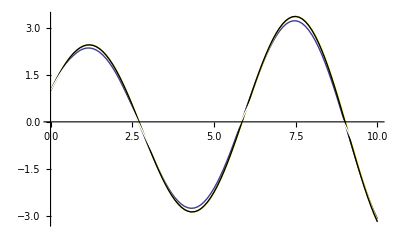

```mathematica
Show[eug,heg,rug,ext]
```

白 : 厳密解、青 : Euler、黄 : heun、黒 : runge - kutta

```mathematica
Clear[f,f1,f2,euler,heun,runge,eulergraph,heungraph,rungegraph,exactgraph,eug,heg,rug,ext]
(*関数等の削除*)
```

## 演習課題4 .2

### (1)

θ''=-Sin[θ],v=θ'より
H'=vv'+θ' Sin[θ]=θ' θ'' + θ' Sin[θ]=θ'(-Sin[θ])+θ' Sin[θ]=0

H'=0よりHは定数関数である. v=θ'より
H (θ, v) = 1/2(θ')^2 - Cos[θ] = C ≥ -1( Cは定数) から
θ'=√(2(C+Cos[θ]))が導かれる. 解軌道(ただしv>0)を以下に示す.

```mathematica
vp[θ_]:=√(2+2 Cos[θ])
```

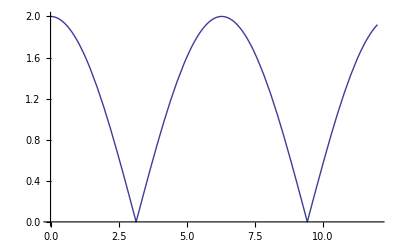

```mathematica
vpg=Plot[vp[θ],{θ,0,12}]
```

### (2)

初期値について: C=1,a1=θ[0] = 0とするとa2=v[0]=θ'[0]=√(2(1Cos[θ[0]]))=2

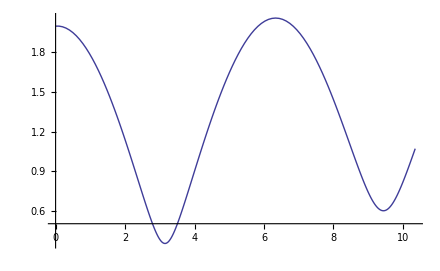

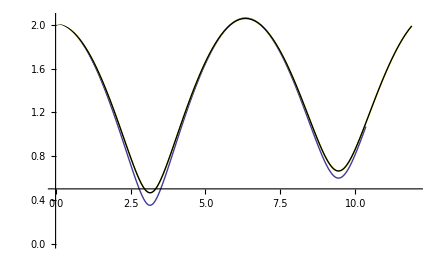

```mathematica
(*関数の設定*)
f[x_,t_]:=-Sin[x];
f1[x1_,x2_,t_]:=x2;
f2[x1_,x2_,t_]:=-Sin[x1];
euler::nonnegativeint="Nmax must be a non-negative integer."; (*Error message*)

(*Euler法*)
euler[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
x1[j_]:=(x1[j]=x1[j-1]+dt f1[x1[j-1],x2[j-1],t]);
x2[j_]:=(x2[j]=x2[j-1]+dt f2[x1[j-1],x2[j-1],t]);
Table[{x1[j],x2[j]},{j,0,Nmax}]
]
];
eulergraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[euler[dt,Nmax,a1,a2],PlotRange->All]

(*Heun法*)
heun[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,k1,k2,m1,m2,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
k1[j_]:=(k1[j]= f1[x1[j],x2[j],t]);
k2[j_]:=(k2[j]= f1[x1[j]+dt k1[j],x2[j]+dt k1[j],t+dt]);
m1[j_]:=(m1[j]=f2[x1[j],x2[j],t]);
m2[j_]:=(m2[j]=f2[x1[j]+dt m1[j],x2[j]+dt m1[j],t+dt]);
x1[j_]:=(x1[j]=x1[j-1]+dt/2(k1[j-1]+k2[j-1]));
x2[j_]:=(x2[j]=x2[j-1]+dt/2(m1[j-1]+m2[j-1]));
Table[{x1[j],x2[j]},{j,0,Nmax}]
]
];
heungraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[heun[dt,Nmax,a1,a2],PlotRange->All,PlotStyle->RGBColor[1,1,0]]

(*Runge-Kutta法*)
runge[dt_,Nmax_,a1_,a2_]:=
Module[{j=0,n,x1,x2,k1,k2,k3,k4,m1,m2,m3,m4,t},
If[Or[Nmax≤0,Not[IntegerQ[Nmax]]],Message[euler::nonnegativeint],
x1[0]:=a1;
x2[0]:=a2;
k1[j_]:=(k1[j]= f1[x1[j],x2[j],t]);
k2[j_]:=(k2[j]= f1[x1[j]+dt/2 k1[j],x2[j]+dt/2 k1[j],t+dt/2]);
k3[j_]:=(k3[j]=f1[x1[j]+dt/2 k2[j],x2[j]+dt/2 k2[j],t+dt/2]);
k4[j_]:=(k4[j]=f1[x1[j]+dt k3[j],x2[j]+dt k3[j],t+dt]);
m1[j_]:=(m1[j]=f2[x1[j],x2[j],t]);
m2[j_]:=(m2[j]=f2[x1[j]+dt/2 m1[j],x2[j]+dt/2 m1[j],t+dt/2]);
m3[j_]:=(m3[j]=f2[x1[j]+dt/2 m2[j],x2[j]+dt/2 m2[j],t+dt/2]);
m4[j_]:=(m4[j]=f2[x1[j]+dt m3[j],x2[j]+dt m3[j],t+dt]);
x1[j_]:=(x1[j]=x1[j-1]+dt/6(k1[j-1]+2 k2[j-1]+2 k3[j-1]+k4[j-1]));
x2[j_]:=(x2[j]=x2[j-1]+dt/6(m1[j-1]+2 m2[j-1]+2 m3[j-1]+m4[j-1]));
Table[{x1[j],x2[j]},{j,0,Nmax}]
]
];
rungegraph[dt_,Nmax_,a1_,a2_]:=ListLinePlot[runge[dt,Nmax,a1,a2],PlotRange->All,PlotStyle->RGBColor[0,0,0]]

(*厳密解*)
ext=Plot[√(2+2 Cos[θ]),{θ,0,12},PlotStyle->RGBColor[1,1,1]];

(*近似具合の比較*)
eug=eulergraph[.05,200,0,2];
heg=  heungraph[.05,200,0,2];
rug=rungegraph[.05,200,0,2];
eulergraph[.05,200,0,2]
Show[eug,heg,rug,ext](*ただしθ-vグラフにしてある.*)
```

白:厳密解、青:Euler、黄:heun、黒:runge-kutta

```mathematica
Clear[f,f1,f2,euler,heun,runge,eulergraph,heungraph,rungegraph,eug,heg,rug,ext]
(*関数等の削除*)
```